### Constants

```mathematica
cost[s_]=269.109*ⅇ^(-0.765 s)+21.538; 
β=0.95;
perfSlowdown[s_]=β^s;
baseRw=0.129*365*24; 
Rw[u_,s_]=baseRw*u*perfSlowdown[s]; 
η=1.2; 
eMax=.165*24*365*.11;
eMin=.030*24*365*.11;
eCost[u_, s_]=(eMin+u(eMax-eMin))η^s;
Qstd=100;
Qfarm=10;
totalCap=10000;
Rb=.;
```

## Lazy PoET

### Useful work

```mathematica
perCPUCost[s_]=eCost[1, s]+Qstd+cost[s];
revUseful[s_]=Rw[1, s]-perCPUCost[s];
{rev,bestS}=Maximize[{revUseful[s],s>0,s<10},s];
bestS=s/.bestS
usefulCPUCount=totalCap/perCPUCost[bestS]
totalUsefullRev=rev*usefulCPUCount
```

1.07964

23.0976

14695.1

### Farming

```mathematica
perCPUCost[s_]=eCost[0, s]+Qfarm+cost[s];
revFarming[s_]=Rb-perCPUCost[s];
{revRb0,bestS}=Maximize[{revFarming[s]/.{Rb->0},s>0,s<10},s];(* Rb doesn't matter for this optimization *)
bestS=s/.bestS;
farmingCPUCount=totalCap/perCPUCost[bestS];
totalFarmingRev=revFarming[bestS]*farmingCPUCount;
```

### Waste

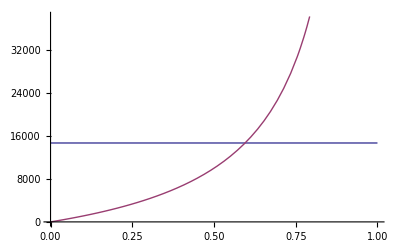

{{usefulRatio→0.595061}}

```mathematica
annualCryptoRev=10^6;
operatorCount=100; 
perCPURev=annualCryptoRev/((1-usefulRatio) operatorCount farmingCPUCount);
Plot[{totalUsefullRev,totalFarmingRev /.Rb->perCPURev},{usefulRatio,0,1}]
NSolve[totalUsefullRev==totalFarmingRev /.Rb->perCPURev,usefulRatio]
```